Université Pierre et Marie Curie |                                                                          | UE 4M062 Mathematica

__________________________________________________________________________

M 1 : Introduction à Mathematica
__________________________________________________________________________

## Exercices

Le fichier doit être renommé exactement comme ceci :
	M1VotrenomPrenom.nb
Cela permet à vos enseignants de s’y retrouver et de ne pas avoir à renommer tous les fichiers. Merci.
	Votrenom avec une seule majuscule
	Prenom avec une seule majuscule
	Pas de blanc, ni souligné, ni accent, ni symbole particulier
Ce fichier doit être déposé sur MOODLE à la fin de la séance, et/ou avant la fin de la semaine de la séance.

NB : Ce fichier comprend PLUSIEURS pages ! qui sont toutes à traiter !!

## I. Interface

### A. Mise en forme

#### 1. Les cellules et leur hiérarchie

Reproduire avec l’Interface de Mathematica la présentation suivante :

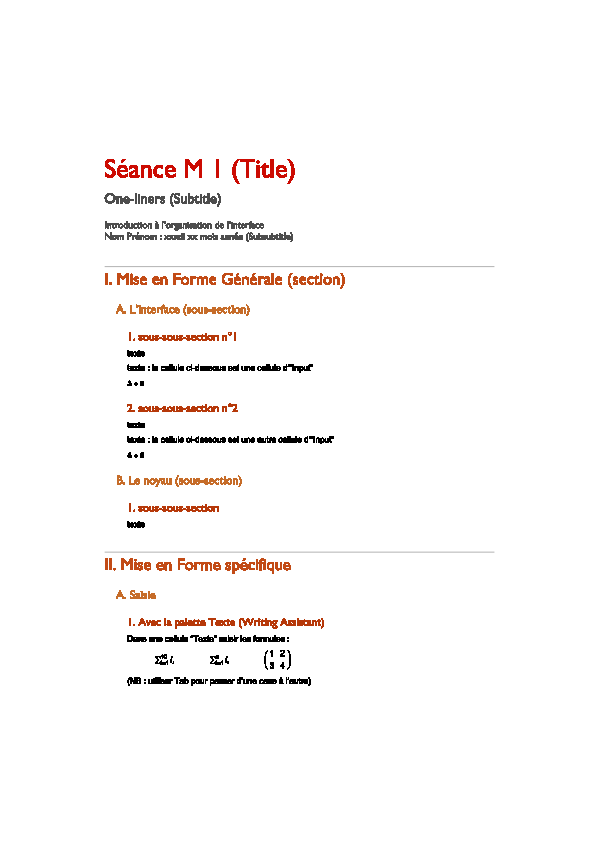

## II. Un tour introductif

→ Expliquer ce qui se passe quand vous validez les cellules : Réfléchissez et donner par écrit les propriétés du logiciel. Les solutions sont données dans les cellules cachées de M1IntroductionMMaTxt.nb

### A. Opérations de base (symboliques avec précision arbitraire)

```mathematica
Bonjour!
```

#### 1. Élémentaire

```mathematica
1+1
```

```mathematica
4a+5a
```

```mathematica
Cos[Pi]
```

```mathematica
Cos[x] /. x -> π
```

```mathematica
3x + 2 x
```

#### 2. Les trois opérations :

```mathematica
31 5
315/14
3^100
```

#### 3. Valeurs numériques approchées N[] :

```mathematica
N[315/14]
N[3^100]
N[3^100, 20]
```

#### 4. Quelques tests utiles à partir de calcul de puissances pour comprendre

```mathematica
3^100;//AbsoluteTiming
```

```mathematica
3^1000;//AbsoluteTiming
```

```mathematica
3^10000;//AbsoluteTiming
```

```mathematica
3^100000;//AbsoluteTiming
```

```mathematica
3^1000000;//AbsoluteTiming
```

```mathematica
3^1000000;//AbsoluteTiming
```

```mathematica
3^10000000;//AbsoluteTiming
```

```mathematica
3^100000000;//AbsoluteTiming
```

```mathematica
3^1000000000;//AbsoluteTiming
```

```mathematica
N[3^100000000];//AbsoluteTiming
N[3.^100000000]//AbsoluteTiming
```

#### 5. Exemples récapitulatifs

```mathematica
N [π]
```

```mathematica
π //N
```

```mathematica
N[π,30]
```

```mathematica
N[π,2000]
```

### B. Opérations de base (numériques)

```mathematica
(10.2-3.1)*6.2/2.9
```

```mathematica
(2+3I)*(4-5I)
```

### C. Nombres et Fonctions élémentaires

#### 1. Quelques constantes mathématiques

→ Saisir dans une cellule input (sans faire de copier coller !!!)

- le nombre π

- le nombre e

- le nombre imaginaire i

- l'infini ∞ :

#### 2. Quelques fonctions mathématiques

Mathematica dispose de nombreuses fonctions prédéfinies dont le nom suit la règle Nom[] :

→ Comment écrit-on dans une cellule input (sans faire de copier coller non plus !!!) les fonctions suivantes :

- racine carrée : √x

- exponentielle : e^x

- logarithme népérien : ln(x)

- logarithme en base b : log_b(x)  (le plus souvent, b=10)

- fonctions trigonométriques :

- fonctions trigonométriques inverses :

- valeur absolue : |x|

- factorielle : n !

→ Sélectionnez la fonction Cos[] et tapez sur F1 (sous PC) ou ⌘ F (sous Mac) pour afficher la page d'aide de cette fonction.

→ Explorez d’autres fonctions avec la rubrique SEE ALSO “ref/ArcCos”

→ Revenez à la page d’aide précédente, et explorez TUTORIALS “tutorial/SomeMathematicalFunctions” qui donne une petite liste des fonctions élémentaires

→ Revenez à la page d’aide précédente, et explorez MORE ABOUT  “guide/SomeMathematicalFunctions” qui donne la liste des fonctions élémentaires

### D. Fonctions

#### 1. Programmation procédurale et fonctionnelle

#### 2. Mode d’utilisation d’une fonction

En dehors de la notation fonctionnel standard Nom[argument1, argument2, ...], il y a trois façons d’utiliser ou de noter les fonctions :
		Prefix
		Infix
		Postfix

→ Quelles sont les notations Infix pour l’addition “+“ , la multiplication “*”, la soustraction “-”, la division “/”, la puissance, →,   /. .... ?

#### 3. Composition de fonctions

→ Saisir dans une cellule “Input”, et constater que la hiérarchie d’indentation est automatiquement respectée à chaque retour à la ligne :

Plot[
 Cos[x],
 {x, -2 π, 2 π}
 ]

Idem...

Manipulate[
 Plot[
  Cos[a x + b],
  {x, -2 π, 2 π}
  ],
 {a, 1, 10},
 {b, 0, 2 π}
 ]

→ Puis jouez avec les curseurs !

#### 4. Arguments et Options des Fonctions : tracer de courbes

Les fonctions ont généralement des arguments obligatoires, et un certain nombre d’Options que l’on peut ou non rajouter pour préciser la fonction. Étudions la fonction très utile Plot[] au travers des exemples suivants :

→ Tracer, ⅇ^-x Sin[2 π x]

→ Idem en rajoutant en option AxesLabel→{“Time”,”Ampl.”}, pour spécifier les axes.
Elle consiste à remplir avec les contenus donnés dans la liste {“Time”,”Ampl.”} la variable AxesLabel :

→ Tracé de plusieurs fonctions sur le même graphe au moyen d’une liste de fonctions :
		 { ⅇ^-x Sin[2 π x],Exp[-x],-Exp[-x] }

→ Mettez des couleurs

#### 5. Définition de nouvelle fonction par l’utilisateur

→ Sur le modèle de la fonction f(x)=(a x)/(b+x), définissez la fonction h(x)=(a x^4)/(b + x^4), pour cela écrire, puis valider la fonction pour qu’elle soit connue du noyau :

#### 6. Éléments d’étude de fonction

→ Calcul de la dérivée première de h :

→ Quelle est la notation fonctionnelle de la dérivation ‘ ?
→ Expliquer comment facilement calculer la dérivée cinquième.

→ Calcul des asymptotes :

→ Calcul de valeurs particulières :

→ Calcul de valeurs particulières par résolution d’équations :
recherchez la valeur de s pour laquelle h[s] est la moitié de la valeur maximale atteignable.

```mathematica
Solve[h[s]==a/2,s]
```

→ Tracer la courbe de h(x) pour a et b valant respectivement 10.0 et 5.0 dans une région pertinente du plan :

→ Est-ce que la fonction h(x) a des singularités (comme la fonction f(x) de ?

→ Montrer que h conserve sa définition symbolique :

### E. Graphiques 2D, 3D, sons et animations

#### 1. Représentation graphique

```mathematica
Plot[Sin[10000/t],{t,0,4000}]
```

Mais on arrive toujours à mettre le système en difficulté (Expliquer pourquoi ?):

```mathematica
Plot[Sin[10000/t],{t,0,40}]
```

#### 2. Représentation sonore

On peut d’ailleurs l’écouter, pour ce convaincre de la pathologie de la fonction en ce point. On remarquera que les singularités du type 1/0 ne sont pas un obstacle, ce qui est très appréciable.

```mathematica
Play[Sin[10000/t],{t,-2,-0.001}]
```

-Graphics-

#### 3. Tracé de fonction en 3 dimensions - Animation 3D

Sur le modèle de II.E.3, tracer une fonction simple en 3D.
En faire ensuite un Manipulate.